## Introduction

How many lattice space groups? How does their number increase with dimension?

A lattice space group has elements (rotations/reflections R, translations/offsets D).
x’ = R.x + D
The R’s form a group, a point group for the space.
D = D(lattice) + D(R)
D(lattice = sum over i of n(i) * e(i) where the e(i) are the lattice basis vectors and the n(i) are integers.
D(R) is a function of R.

The lattice has the same number of dimensions as the space
Crystal Families
Crystal Systems
Bravais Lattices - plain vs. centered separate
Abstract Point Groups
Geometric Crystal Classes - Q-classes - crystal + point group 
Arithmetic Crystal Classes - Z-classes - Bravais + point group orientations separate
Space Groups - counting mirror images together
Space Groups Mirrored - counting mirror images separately
Magnetic Space Groups - counting mirror images together
Magnetic Space Groups Mirrored - counting mirror images separately

The lattice may have fewer dimensions than the space

With crystallographic constraints
Special names, by (space dimension, lattice dimension, if magnetic):
n,0 - Crystallographic point groups (geometric crystal classes)
1,1 Magnetic - Frieze
2,1 - Frieze
2,2 - Wallpaper
3,1 - Rod
3,2 - Layer

Without crystallographic constraints
2,0 - infinite families: 2
3,0 - infinite families: 7, extra: 7
3,1 - infinite families: 13

### Examples

0,0D: point: identity group, except for magnetic group {1,-1}

1,0D: point: identity: {1}, reflection: {1, -1}

1,1D: line: one kind of lattice, both point groups

2,0D: point: (finite, size factor n) C(n), D(n), (continuous) SO(2), O(2)
C = cyclic (rotations), D = dihedral (rotations, reflections)

2,1D: frieze: one kind of lattice
- Geometric classes (point groups): C1, C2, D1, D2
- Arithmetic classes (point-group orientations): C1: 1, C2: 1, D1: 2, D2: 1
- Space groups (shifts added to each orientation): C1: 1, C2: 1, D1: 2, 1, D2: 2

2,2D: wallpaper:
- Crystal families, systems: 4: oblique, rectangular, square, hexagonal
- Bravais lattices: 5: rectangular split into plain and centered (rhombic)
- Geometric classes: 10: Obl C1, C2, Rect D1, D2, Sqr C4, D4, Hex C3, D3, C6, D6
- Arithmetic classes: 13: Obl C1, C2, Rect Pln D1, D2, Rect Ctrd D1, D2, Sqr C4, D4, Hex: C3, D3 (2 orientations), C6, D6
- Space groups: 17: Obl C1: 1, C2: 1, Rect Pln D1: 2, D2: 3, Rect Ctrd D1: 1, D2: 1, Sqr C4: 1, D4: 2, Hex: C3: 1, D3: 1, 1, C6: 1, D6: 1

### Sources

Space group - Wikipedia
 https://en.wikipedia.org/wiki/Space_group
Magnetic space group - Wikipedia
https://en.wikipedia.org/wiki/Magnetic_space_group
Each magnetic-group element is a plain space-group element with +1 or -1 added on

Same-dimension lattices:
https://oeis.org/A004032 - Number of n-dimensional crystal families.
https://oeis.org/A004031 - Number of n-dimensional crystal systems.
https://oeis.org/A256413 - Number of n-dimensional Bravais lattices. (me: corrected from A004030)
https://oeis.org/A006226 - Number of abstract n-dimensional crystallographic point groups
https://oeis.org/A004028 - Number of geometric n-dimensional crystal classes.
https://oeis.org/A004027 - Number of arithmetic n-dimensional crystal classes.
https://oeis.org/A004029 - Number of n-dimensional space groups.
https://oeis.org/A006227 - Number of n-dimensional space groups (including enantiomorphs). (me: mirror images)
https://oeis.org/A307292 - Number of black-and-white colored (or proper magnetic) space groups in dimension n, not counting enantiomorphs.
https://oeis.org/A307290 - Number of black-and-white colored (or proper magnetic) space groups in dimension n, counting enantiomorphs.
https://oeis.org/A307291 - Number of colored (or magnetic) space groups in dimension n, including enantiomorphs.

Lower-dimension lattices:
https://oeis.org/A293060 - Triangle read by rows (n >= 0, 0 <= k <= n): T(n,k) = number of k-dimensional subperiodic groups in n-dimensional space, not counting enantiomorphs.
https://oeis.org/A293061 - Triangle read by rows (n >= 0, 0 <= k <= n): T(n,k) = number of k-dimensional subperiodic groups in n-dimensional space, counting enantiomorphs.
https://oeis.org/A293062 - Triangle read by rows (n >= 0, 0 <= k <= n): T(n,k) = number of k-dimensional magnetic subperiodic groups in n-dimensional space, not counting enantiomorphs.
https://oeis.org/A293063 - Triangle read by rows (n >= 0, 0 <= k <= n): T(n,k) = number of k-dimensional magnetic subperiodic groups in n-dimensional space, counting enantiomorphs.

## Data

```mathematica
(* Starting with zero dimensions: point *)
```

```mathematica
(* Latice same dimension as space *)
```

```mathematica
NumSameDimGroups = <|"Crystal Families"->{1,1,4,6,23,32,91},"Crystal Systems"->{1,1,4,7,33,59,251},"Bravais Lattices"->{1,1,5,14,64,189,841},"Abstract Point Groups"->{1,2,9,18,118,239,1594},"Geometric Crystal Classes"->{1,2,10,32,227,955,7103},"Arithmetic Crystal Classes"->{1,2,13,73,710,6079,85308},"Space Groups"->{1,2,17,219,4783,222018,28927915},"Space Groups Mirrored"->{1,2,17,230,4894,222097},"Magnetic Space Groups"->{0,3,46,1156,51987} + 2*{1,2,17,219,4783},"Magnetic Space Groups Mirrored"->{0,3,46,1191,52439}+ 2*{1,2,17,230,4894}|>;
```

```mathematica
MakeDataTriangle[data_] := Module[{ix,num=1,row={},tri={}},
Do[AppendTo[row,data[[ix]]]; If[Length[row]>=num,AppendTo[tri,row];row={};num++],{ix,Length[data]}];
If[Length[row]>0,AppendTo[tri,row]];
tri
]
```

```mathematica
(* Lattice lower dimensions, from 0 to space *)
```

```mathematica
NumLowerDimGroups = <|"Space Groups"->MakeDataTriangle[{1,2,2,10,7,17,32,67,80,219,227,343,1076,1594,4783,955}],"Space Groups Mirrored"->MakeDataTriangle[{1,2,2,10,7,17,32,75,80,230,271,343,1091,1594,4894,955}],"Magnetic Space Groups"->MakeDataTriangle[{2,5,7,31,31,80,122,360,528,1594,1025}],"Magnetic Space Groups Mirrored"->MakeDataTriangle[{2,5,7,31,31,80,122,394,528,1651,1202}]|>;
```

## Analysis

### Same-Dimension Lattices

```mathematica
TableForm[Values[NumSameDimGroups],TableHeadings->{Keys[NumSameDimGroups],Range[0,6]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6
Crystal Families | 1 | 1 | 4 | 6 | 23 | 32 | 91
Crystal Systems | 1 | 1 | 4 | 7 | 33 | 59 | 251
Bravais Lattices | 1 | 1 | 5 | 14 | 64 | 189 | 841
Abstract Point Groups | 1 | 2 | 9 | 18 | 118 | 239 | 1594
Geometric Crystal Classes | 1 | 2 | 10 | 32 | 227 | 955 | 7103
Arithmetic Crystal Classes | 1 | 2 | 13 | 73 | 710 | 6079 | 85308
Space Groups | 1 | 2 | 17 | 219 | 4783 | 222018 | 28927915
Space Groups Mirrored | 1 | 2 | 17 | 230 | 4894 | 222097 | 
Magnetic Space Groups | 2 | 7 | 80 | 1594 | 61553 |  | 
Magnetic Space Groups Mirrored | 2 | 7 | 80 | 1651 | 62227 |  |

```mathematica
Length /@ NumSameDimGroups
```

<|Crystal Families→7,Crystal Systems→7,Bravais Lattices→7,Abstract Point Groups→7,Geometric Crystal Classes→7,Arithmetic Crystal Classes→7,Space Groups→7,Space Groups Mirrored→6,Magnetic Space Groups→5,Magnetic Space Groups Mirrored→5|>

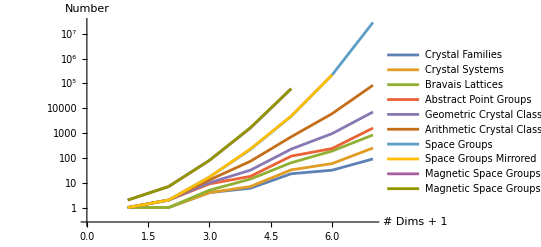

```mathematica
ListLogPlot[Values[NumSameDimGroups],Joined->True,PlotLegends->Keys[NumSameDimGroups],AxesLabel->{"# Dims + 1","Number"}]
```

```mathematica
RatioNext[x_] := Rest[x]/Most[x]
```

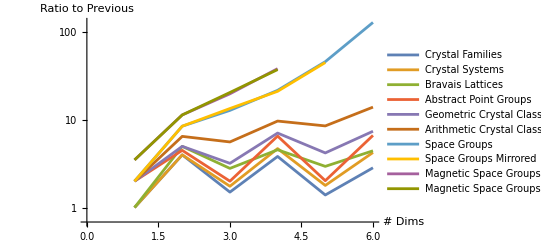

```mathematica
ListLogPlot[RatioNext /@ Values[NumSameDimGroups],Joined->True,PlotLegends->Keys[NumSameDimGroups],AxesLabel->{"# Dims","Ratio to Previous"}]
```

```mathematica
MirrorFraction[NumTogether_List,NumSeparate_List] := Module[{minlen,numtog,numsep},
minlen = Min[Length[NumTogether],Length[NumSeparate]];
numtog = Take[NumTogether,minlen];
numsep = Take[NumSeparate,minlen];
(numsep - numtog)/numtog
]
```

```mathematica
MirrorFraction[NumSameDimGroups["Space Groups"],NumSameDimGroups["Space Groups Mirrored"]] // N
```

{0.,0.,0.,0.0502283,0.0232072,0.000355827}

```mathematica
MirrorFraction[NumSameDimGroups["Magnetic Space Groups"],NumSameDimGroups["Magnetic Space Groups Mirrored"]] // N
```

{0.,0.,0.,0.0357591,0.0109499}

### Lower-Dimension Lattices

```mathematica
MergeLowerDimNums[] := Module[{vals,nvs},
vals = Values[NumLowerDimGroups];
nvs = Length[vals];
Table[Table[If[i>Length[vals[[k]]],Null,If[j>Length[vals[[k,i]]],Null,vals[[k,i,j]]]],{k,nvs}],{i,Length[vals[[1]]]},{j,Length[vals[[1,i]]]}]
]
```

Each entry in the table is a column with entries for plain space groups and magnetic ones, both plain and mirrored (mirror images counted together or separately)

```mathematica
Keys[NumLowerDimGroups]
```

{Space Groups,Space Groups Mirrored,Magnetic Space Groups,Magnetic Space Groups Mirrored}

```mathematica
(* Number labels are number of dimensions: the space, the lattice *)
```

```mathematica
TableForm[MergeLowerDimNums[],TableHeadings->{Range[0,5],Range[0,4]}]
```

| 0 | 1 | 2 | 3 | 4
0 | 1
1
2
2 |  |  |  | 
1 | 2
2
5
5 | 2
2
7
7 |  |  | 
2 | 10
10
31
31 | 7
7
31
31 | 17
17
80
80 |  | 
3 | 32
32
122
122 | 67
75
360
394 | 80
80
528
528 | 219
230
1594
1651 | 
4 | 227
271
1025
1202 | 343
343
Null
Null | 1076
1091
Null
Null | 1594
1594
Null
Null | 4783
4894
Null
Null
5 | 955
955
Null
Null |  |  |  |

There is a rather curious pattern: no extra mirror images for (space dimensions) - (lattice dimensions) even.

```mathematica
TriangularSheet[tridata_] := Module[{n,verts,ix,vertixs,triangles},
(* Make the vertices *)
n = Length[tridata];
verts = Flatten[Table[{i,j,tridata[[i,j]]},{i,n},{j,Length[tridata[[i]]]}],1];
ix = 1;
(* Index pair to vertex *)
Do[vertixs[i,j] = ix; ix++,{i,n},{j,1,i}];
triangles = Map[vertixs@@ #&,Flatten[Table[{{{i,j},{i+1,j},{i+1,j+1}},If[j<i,{{i,j},{i+1,j+1},{i,j+1}},Nothing]},{i,n-1},{j,1,i}],2],{2}];
GraphicsComplex[verts,Polygon[triangles]]
]
```

```mathematica
Graphics3D[{TriangularSheet[Log10[N[Most[NumLowerDimGroups["Space Groups"]]]]],TriangularSheet[Log10[N[Most[NumLowerDimGroups["Magnetic Space Groups"]]]]]},SphericalRegion->True,Axes->True,AxesLabel->{"Space #D+1","Lattice #D+1","Log10 Value"}]
```

-Graphics3D-

```mathematica
(* Magnetic-to-plain ratio*)
```

```mathematica
Graphics3D[TriangularSheet[N[Take[NumLowerDimGroups["Magnetic Space Groups"],4]/Take[NumLowerDimGroups["Space Groups"],4]]],SphericalRegion->True,Axes->True,AxesLabel->{"Space #D+1","Lattice #D+1","Ratio"}]
```

-Graphics3D-

```mathematica
MirrorFraction[NumLowerDimGroups["Space Groups"],NumLowerDimGroups["Space Groups Mirrored"]] // N
```

{{0.},{0.,0.},{0.,0.,0.},{0.,0.119403,0.,0.0502283},{0.193833,0.,0.0139405,0.,0.0232072},{0.}}

```mathematica
MirrorFraction[NumLowerDimGroups["Magnetic Space Groups"],NumLowerDimGroups["Magnetic Space Groups Mirrored"]] // N
```

{{0.},{0.,0.},{0.,0.,0.},{0.,0.0944444,0.,0.0357591},{0.172683}}